# Análisis de las unidades de tiempo

People=10,50,100,500,1000
Time=100,100,1000,1000,10000
Capacity=2,4,6,8,10

```mathematica
SetDirectory[NotebookDirectory[]];
```

## Cargar las redes (1 ejecución)

```mathematica
capacity=Range[2,10,2];
peopleVals={10,50,100,500,1000};
timeVals={100,100,1000,1000,10000};
nets=Table[Import[StringJoin["graphs/model-v3/1/","network-",IntegerString[peopleVals[[i]]],"-",IntegerString[capacity[[j]]],"-",IntegerString[timeVals[[i]]],".g6"]],{i,1,5,1},{j,1,5,1}];
```

### Grado de los nodos

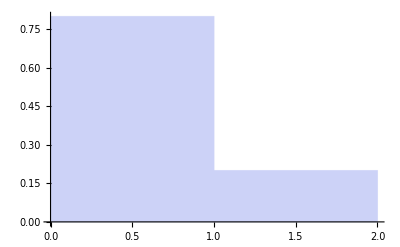
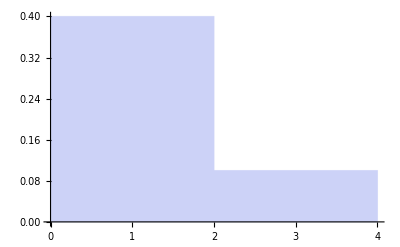
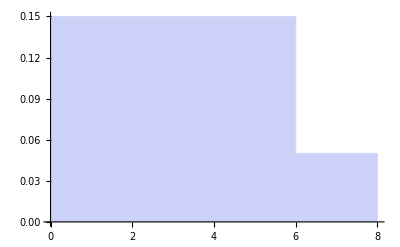
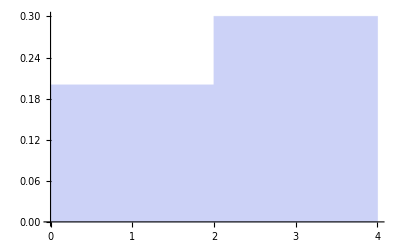
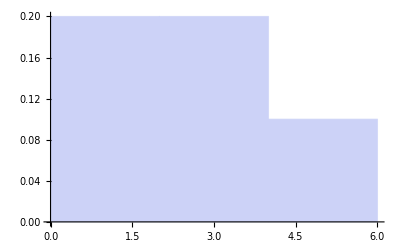
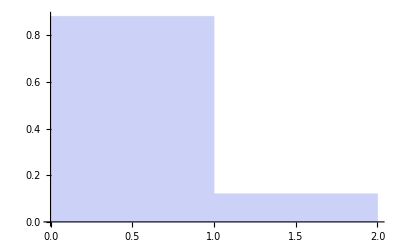
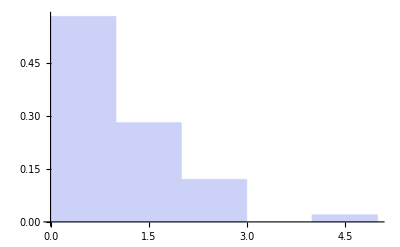
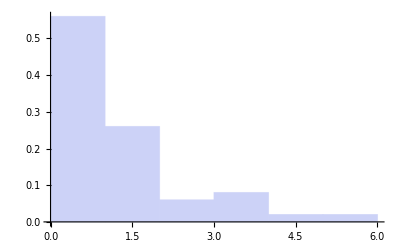
{{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}}

```mathematica
Table[Histogram[VertexDegree[people100[[i,j]]],Automatic,"PDF"],{i,1,Length[people100],1},{j,1,Length[people100[[i]]],1}]
```

### capacity vs clustering coefficient

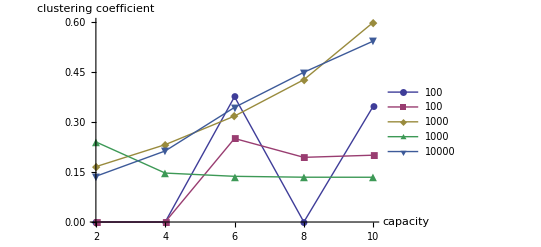

```mathematica
clustering=Table[Map[GlobalClusteringCoefficient,nets[[i]]],{i,1,5,1}];
dataPlot=Table[Table[{capacity[[k]],clustering[[p,k]]},{k,1,5,1}],{p,1,5,1}];
ListLinePlot[dataPlot,PlotLegends->timeVals,AxesLabel->{"capacity","clustering coefficient"},PlotMarkers->Automatic]
```

### time vs clustering coefficient

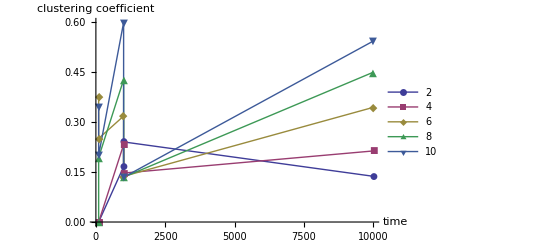

```mathematica
clustering2=Table[Map[GlobalClusteringCoefficient,nets[[i]]],{i,1,5,1}];
dataPlot2=Table[Table[{timeVals[[t]],clustering2[[t,k]]},{t,1,5,1}],{k,1,5,1}];
ListLinePlot[dataPlot2,PlotLegends->capacity,AxesLabel->{"time","clustering coefficient"},PlotMarkers->Automatic]
```

### people vs clustering coefficient

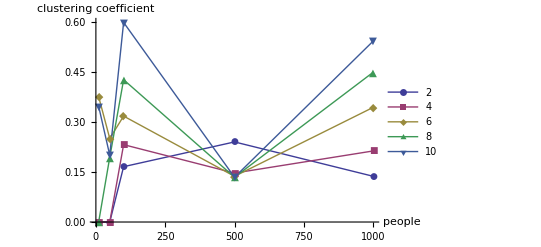

```mathematica
clustering3=Table[Map[GlobalClusteringCoefficient,nets[[i]]],{i,1,5,1}];
dataPlot3=Table[Table[{peopleVals[[p]],clustering3[[p,k]]},{p,1,5,1}],{k,1,5,1}];
ListLinePlot[dataPlot3,PlotLegends->capacity,AxesLabel->{"people","clustering coefficient"},PlotMarkers->Automatic]
```

### capacity vs average path length